```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

#### Range of densities

```mathematica
{triggermass[0.85],triggermass[1.37]}
```

{0.00337513,0.0000124363}

```mathematica
{Massreverse[0.85],Massreverse[1.25],Massreverse[1.37]}
```

{7.1606,8.46005,9.50943}

```mathematica
{Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->7.16},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->8.46},Convert[10^logρ Gram/Centimeter^3 1/(12 Giga ElectronVolt)*1Giga ElectronVolt/ProtonMass,1/Centimeter^3]/.{logρ->9.5}}
```

{(7.20147×10^29)/Centimeter^3,(1.43688×10^31)/Centimeter^3,(1.57551×10^32)/Centimeter^3}

```mathematica
6*{(7.201468136264897*^29)/Centimeter^3,(1.4368817984738546*^31)/Centimeter^3,(1.5755095624615844*^32)/Centimeter^3}
```

{(4.32088×10^30)/Centimeter^3,(8.62129×10^31)/Centimeter^3,(9.45306×10^32)/Centimeter^3}

```mathematica
Convert[9.453057374769507*^32 Centimeter^-3(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]//N
```

7.56245 ElectronVolt^3 Mega^3

WD data

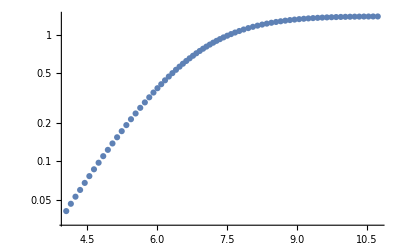

```mathematica
ListLogPlot[WD]
```

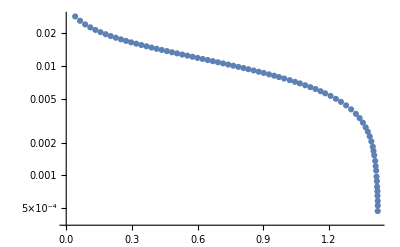

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Convert[Radplot[1.25]SolarRadius,Kilo Meter]
```

3328.47 Kilo Meter

```mathematica
Convert[Radplot[0.85]SolarRadius,Kilo Meter]
```

6392.93 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.00230345 √(1/Radplot[1.25])

```mathematica
vesc[0.85]
```

0.0198191

```mathematica
Radplot[1.40]
```

0.00185935

```mathematica
vesc[1.42]
```

0.086269

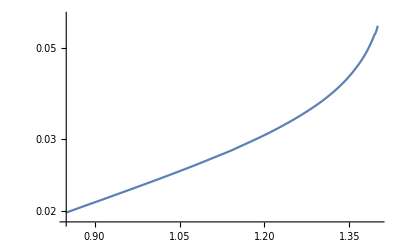

```mathematica
LogPlot[vesc[M],{M,0.85,1.4}]
```

#### λ_T as function of WD mass

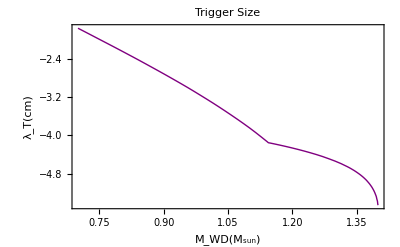

```mathematica
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.6,0.01}]];
Plot[Log10[triggermass[M]],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### E_boom (GeV) as function of WD mass

```mathematica
10^logρ Convert[Gram/Centimeter^3 1/(12 Giga ElectronVolt/SpeedOfLight^2)*(200 Mega ElectronVolt Fermi)^3,(Mega ElectronVolt)^3]*(1/(Mega ElectronVolt))^3
```

3.73973×10^-10 10^logρ

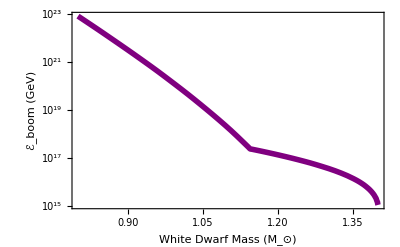

```mathematica
nionMeV[M_]:=Convert[10^Massreverse[M] Gram/Centimeter^3*SpeedOfLight^2/(12Giga ElectronVolt)*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]*1/(Mega ElectronVolt)^3
nionMeV2[logρ_]:=3.7397260789901873*^-10 10^logρ
eboom[M_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(triggermass[M](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV[M],Z->6})]
eboomdensity[logρ_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(trigger[10^logρ](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV2[logρ],Z->6})]
eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.40,0.01}],InterpolationOrder->1][mdm]
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,None},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_⊙)","ℰ_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

#### How much of the WD detector should we observe?

```mathematica
restrict=1/2;
```

#### SN information

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
integralcollision[logmdm_]:=Re[NIntegrate[vesc[x]^3 (4π)/3(Radplot[x]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlesscollision=Convert[snrate*((10^logmdm Giga ElectronVolt)/(0.4 (Giga ElectronVolt)/Centimeter^3))^2((10^-3 SpeedOfLight)^2)/(SpeedOfLight^3*SolarRadius^3),Centimeter^2] 1/Centimeter^2;
```

```mathematica
integraldecay[logmdm_]:=Re[NIntegrate[vesc[1.25] (4π)/3(Radplot[1.25]*restrict)^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlessdecay=Convert[1/snrate (0.4(Giga ElectronVolt)/Centimeter^3)/(10^logmdm Giga ElectronVolt)(SpeedOfLight SolarRadius^3)/(10^-3 SpeedOfLight),Giga Year] 1/(Giga Year);
```

#### DM Wind - Collision Constraints

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3(Rwd*restrict)^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->eboom[1.25]
```

1.01577×10^-20

```mathematica
σobsNuStar/.logmdm->eboom[1.25]
```

1.62523×10^-27

```mathematica
eboom[1.4]
```

15.0338

```mathematica
(Log10[unitlesscollision 1/integralcollision[15.04]]/.logmdm->15.04)
```

-16.6446

```mathematica
Table[{logmdm,Log10[unitlesscollision 1/integralcollision[logmdm]]},{logmdm,15.04,24,0.1}];
```

$Aborted

```mathematica
SNlist={{15.04,-16.10406176129751},{15.139999999999999,-17.172399046810057},{15.239999999999998,-17.291977329160385},{15.34,-17.292168309046474},{15.44,-17.24315844948377},{15.54,-17.204526058483797},{15.639999999999999,-17.214178641793193},{15.739999999999998,-17.191167884183987},{15.84,-17.19198571688968},{15.94,-17.18622987721764},{16.04,-17.1869120551312},{16.14,-17.199547138311367},{16.24,-17.218634919596216},{16.34,-17.250999604393925},{16.439999999999998,-17.294111333374023},{16.54,-17.347238299142795},{16.64,-17.41419384266277},{16.74,-17.482208618206958},{16.84,-17.562068159874723},{16.939999999999998,-17.65044375555382},{17.04,-17.743089164157265},{17.14,-17.839315526309125},{17.24,-17.937722097954524},{17.34,-18.038769966686523},{17.439999999999998,-17.975451222862187},{17.54,-17.849595363164497},{17.64,-17.7110444768282},{17.74,-17.572148396772256},{17.84,-17.432690310794737},{17.939999999999998,-17.293532988828026},{18.04,-17.15408243113624},{18.14,-17.015483957841823},{18.24,-16.87671637990075},{18.34,-16.738976164649046},{18.439999999999998,-16.60085088332797},{18.54,-16.46334864820152},{18.64,-16.325318605592454},{18.74,-16.18738392111567},{18.84,-16.049068491692918},{18.939999999999998,-15.91049875914166},{19.04,-15.77172048843425},{19.14,-15.632431729604466},{19.24,-15.49295363259842},{19.34,-15.35287219889305},{19.439999999999998,-15.212495521044529},{19.54,-15.07176863984791},{19.64,-14.930598726671715},{19.74,-14.78953668182063},{19.84,-14.64797553376806},{19.939999999999998,-14.50623649653608},{20.04,-14.364021599992506},{20.14,-14.22115719133776},{20.24,-14.077599905133166},{20.34,-13.93333797053565},{20.439999999999998,-13.788402876276049},{20.54,-13.643150562657862},{20.64,-13.497413050434492},{20.74,-13.351457259907141},{20.84,-13.205198832750712},{20.939999999999998,-13.058292134333728},{21.04,-12.910782296523378},{21.14,-12.762505718485759},{21.24,-12.613412245599832},{21.34,-12.463559876734976},{21.439999999999998,-12.313036262805307},{21.54,-12.16175487599537},{21.64,-12.00974471698437},{21.74,-11.857004540104834},{21.84,-11.703381486648412},{21.939999999999998,-11.54887739522484},{22.04,-11.393399255587388},{22.14,-11.2370535738019},{22.24,-11.07162583960384},{22.34,-10.871625839603837},{22.439999999999998,-10.671625839603841},{22.54,-10.471625839603838},{22.64,-10.271625839603836},{22.74,-10.07162583960384},{22.84,-9.871625839603837},{22.939999999999998,-9.671625839603841},{23.04,-9.471625839603838},{23.14,-9.271625839603836},{23.240000000000002,-9.071625839603833},{23.34,-8.871625839603837},{23.439999999999998,-8.671625839603841},{23.54,-8.471625839603838},{23.64,-8.271625839603836},{23.740000000000002,-8.071625839603833},{23.84,-7.871625839603837},{23.939999999999998,-7.671625839603841}};
```

```mathematica
collisionSNwhole[logmdm_]:=If[logmdm≥24,Interpolation[SNlist][23.5]+2(logmdm-23.5),Interpolation[SNlist][logmdm]]
SNcollision=Plot[collisionSNwhole[logmdm],{logmdm,15.04,30},PlotStyle->{Black,Thick}];
```

```mathematica
eboomlimitcollisionf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-35,10}];
eboomlimitcollisionf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{-35,-2}];
collisionlimitSN=Plot[( 100 Sign[x-eboom[1.40]]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.0065],Black}],PlotRange->{-16.104061761297505,5}];
RXcollision=Plot[Log10[σobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];
XLabelCollision={{14,"10^14"},{16,"10^16"},{18,"10^18"},{20,"10^20"},{22,"10^22"},{24,"10^24"},{26,"10^26"},{28,"10^28"},{30,"10^30"}};
YLabelCollision={{-30,"10^-30"},{-25,"10^-25"},{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"}};
canvascollisionf1=Plot[-100,{logmdm,15.1,30},Frame->True,FrameTicks->{{YLabelCollision,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(DM - DM) (cm^2)"},PlotRange->{-28,1},Axes->None];
```

```mathematica
SNcollisionregionplot=RegionPlot[{Log10[σHalo]>σ>collisionSNwhole[logmdm]},{logmdm,15.04,30},{σ,-20,10}];
```

InterpolatingFunction::dmval: Input value {23.9963} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9471} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9717} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

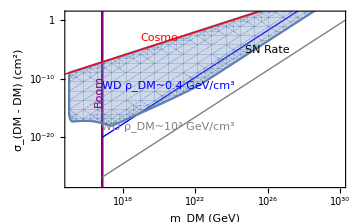

```mathematica
collisionobservation=Show[canvascollisionf1,eboomlimitcollisionf1,RXcollision, NuStarcollision,SNcollisionregionplot,σHaloplot,Graphics[Inset[Style["WD ρ_DM~0.4 GeV/cm^3",Small,Blue,FontFamily->"Helvetica"],{20.5,-11.2},{0,0},10,{1,1/1.5}]],Graphics[Inset[Style["WD ρ_DM~10^3 GeV/cm^3",Small,Gray,FontFamily->"Helvetica"],{20.5,-18.1},{0,0},10,{1,1/1.5}]],Graphics[Inset[Style["SN Rate",Small,Black,FontFamily->"Helvetica"],{26,-5},{0,0},10,{1,1/1.5}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{16.7,-12},{0,0},10,{0,1}]],Graphics[Inset[Style["Cosmo",Small,Red,FontFamily->"Helvetica"],{20,-3},{0,0},10,{1,1/3}]],ImageSize->Medium]
```

#### DM Wind - Decay Constraints

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3(Rwd restrict)^3;
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->eboom[1.25]
```

3.15562×10^11

```mathematica
τobsNuStar/.logmdm->eboom[1.25]
```

7.88906×10^14

```mathematica
Log10[unitlessdecay integraldecay[15.04]]/.logmdm->15.04
```

5.06183

```mathematica
SNlistdecay=Table[{logmdm,Log10[unitlessdecay integraldecay[logmdm]]},{logmdm,15.04,24,0.1}];
```

```mathematica
SNlistdecay
```

```mathematica
SNlistdecay={{15.04,5.061829204847497},{15.139999999999999,6.214449275371579},{15.239999999999998,6.420589455810837},{15.34,6.510461040359902},{15.44,6.551544112979498},{15.54,6.598983262457922},{15.639999999999999,6.6856613499137305},{15.739999999999998,6.739440702499228},{15.84,6.810654823208336},{15.94,6.87409651751223},{16.04,6.941603890234163},{16.14,7.018476255467032},{16.24,7.100924160863706},{16.34,7.195626583705712},{16.439999999999998,7.301378901121159},{16.54,7.41810524681221},{16.64,7.54973122020263},{16.74,7.685465761743471},{16.84,7.834576812918031},{16.939999999999998,7.994203637136746},{17.04,8.160348433582529},{17.14,8.33212650625868},{17.24,8.508515604189945},{17.34,8.68944064906932},{17.439999999999998,8.717377216011768},{17.54,8.68690718694907},{17.64,8.644664523237047},{17.74,8.602230683947052},{17.84,8.559395960846766},{17.939999999999998,8.51696563349105},{18.04,8.474353931738168},{18.14,8.43261081928965},{18.24,8.390759744502407},{18.34,8.349933933008959},{18.439999999999998,8.308791626797166},{18.54,8.26830106438931},{18.64,8.227370599695131},{18.74,8.186595386189007},{18.84,8.145522491925444},{18.939999999999998,8.104275333651207},{19.04,8.06289985152446},{19.14,8.02110489008738},{19.24,7.979195254970561},{19.34,7.9367661371903155},{19.439999999999998,7.894108112253941},{19.54,7.851166934406992},{19.64,7.8078527462422915},{19.74,7.764699029448229},{19.84,7.721122618226387},{19.939999999999998,7.677434099756068},{20.04,7.633345861905258},{20.14,7.5886904443392265},{20.24,7.543425648510447},{20.34,7.497537414166098},{20.439999999999998,7.451052903816492},{20.54,7.404311306028331},{20.64,7.357146431243585},{20.74,7.309819417282067},{20.84,7.262253460809001},{20.939999999999998,7.214119075568504},{21.04,7.165459681707677},{21.14,7.116111599627434},{21.24,7.066012862544948},{21.34,7.015215771441305},{21.439999999999998,6.963808844192963},{21.54,6.911716347424954},{21.64,6.858982016750252},{21.74,6.805603420150687},{21.84,6.751421635511648},{21.939999999999998,6.6964179758545805},{22.04,6.640493313700964},{22.14,6.583753107612602},{22.24,6.518052789531721},{22.34,6.418052789531719},{22.439999999999998,6.3180527895317224},{22.54,6.218052789531721},{22.64,6.11805278953172},{22.74,6.018052789531722},{22.84,5.91805278953172},{22.939999999999998,5.8180527895317224},{23.04,5.718052789531721},{23.14,5.61805278953172},{23.240000000000002,5.518052789531718},{23.34,5.41805278953172},{23.439999999999998,5.3180527895317224},{23.54,5.218052789531721},{23.64,5.11805278953172},{23.740000000000002,5.018052789531717},{23.84,4.91805278953172},{23.939999999999998,4.8180527895317224}};
```

```mathematica
decaySNwhole[logmdm_]:=If[logmdm≥24,Interpolation[SNlistdecay][23.5]-(logmdm-23.5),Interpolation[SNlistdecay][logmdm]]
```

```mathematica
SNdecay=Plot[decaySNwhole[logmdm],{logmdm,15.04,30},PlotStyle->{Black,Thick}];
```

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,eboom[1.25],35},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,eboom[1.25],35},PlotStyle->{Gray,Thick}];eboomlimitdecayf1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{0,20}];
eboomlimitdecayf2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-3])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{3.5,20}];
decaylimitSN=Plot[(100 Sign[x-eboom[1.4]]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.006],Black}],PlotRange->{-10,5.061829204847496}];
YLabelDecay={{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"}};
canvasdecayf1=Plot[-100,{logmdm,15,28},Frame->True,FrameTicks->{{YLabelDecay,None},{XLabelCollision,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "τ_DM (Gyr)"},PlotRange->{1.3,15},Axes->None];
```

```mathematica
SNdecayregionplot=RegionPlot[{2≤τ≤decaySNwhole[logmdm]},{logmdm,15.04,30},{τ,0,10}];
```

InterpolatingFunction::dmval: Input value {23.9963} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.9471} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

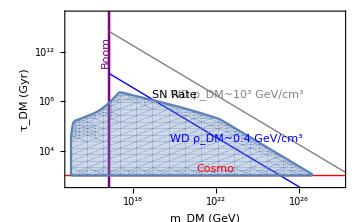

```mathematica
decayobservation=Show[canvasdecayf1,eboomlimitdecayf1,RXdecay,NuStardecay,SNdecayregionplot,τCosmoplot,Graphics[Inset[Style["WD ρ_DM~0.4 GeV/cm^3",Small,Blue,FontFamily->"Helvetica"],{23,5},{0,0},10,{1,-1/1.5}]],Graphics[Inset[Style["WD ρ_DM~10^3 GeV/cm^3",Small,Gray,FontFamily->"Helvetica"],{23,8.5},{0,0},10,{1,-1/1.5}]],Graphics[Inset[Style["SN Rate",Small,Black,FontFamily->"Helvetica"],{20,8.5},{0,0},10,{1,-1/10}]],Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{16.7,12},{0,0},10,{0,1}]],Graphics[Inset[Style["Cosmo",Small,Red,FontFamily->"Helvetica"],{22,2.5},{0,0},10,{1,0}]],ImageSize->Medium]
```

#### DM Capture - Constraints

```mathematica
nionMeV[1.25] MeV^3*(200 MeV 10^-13 cm)^-3
```

(1.34833×10^31)/cm^3

```mathematica
Rth=FullSimplify[((T Mpl^2)/(mdm (nion mc)))^(1/2)*0.2GeV 10^-15 m/.{T->10^-6 GeV,Mpl->10^19 GeV,mdm->GeV 10^logmdm,nion->nionMeV[1.25] MeV^3(GeV/(10^3 MeV))^3,mc->12GeV},GeV>0]*1/m;
```

```mathematica
Rth/.logmdm->16
```

0.0005559

```mathematica
Mcore=FullSimplify[(nion mc) 4 Pi/3(((T Mpl^2)/(mdm (nion mc)))^(1/2))^3/.{T->10^-6 GeV,Mpl->10^19 GeV,mdm->GeV 10^logmdm,nion->nionMeV[1.25] MeV^3(GeV/(10^3 MeV))^3,mc->12GeV},GeV>0];
```

```mathematica
Mcore/.logmdm->16
```

1.16428×10^29 GeV

```mathematica
ρwd (4Pi)/3(((T Mpl^2)/(mdm ρwd))^(1/2))^3 1/mdm(ρdm/mdm π Rwd^2 vesc^2/v)^-1
```

(4 v ((Mpl^2 T)/(mdm ρwd))^(3/2) ρwd)/(3 Rwd^2 vesc^2 ρdm)

```mathematica
tcollect=FullSimplify[ρwd (4Pi)/3(((T Mpl^2)/(mdm ρwd))^(1/2))^3 1/mdm(ρdm/mdm π Rwd^2 vesc^2/v)^-1 0.2GeV 10^-15 m s/(3 10^8 m)/.{mdm->GeV 10^logmdm,v->10^-3,ρdm->0.4 GeV/cm^3*(0.2GeV*10^-13 cm)^3,vesc->vesc[M],ρwd->nionMeV[M] MeV^3 12GeV (GeV/(10^3 MeV))^3,Mpl->10^19 GeV,τ->5 10^9 yr *(Pi 10^7 s/yr)(3 10^10 cm/s)(0.2GeV 10^-13 cm)^-1,Rwd->Radplot[M]sradius (7 10^10 cm/sradius) (0.2GeV 10^-13 cm)^-1,T->10^-6 GeV}/.M->1.25,GeV>0]*1/s;
```

```mathematica
tcollect/.logmdm->16
```

24.8388

```mathematica
tdrift=FullSimplify[Rwd/Sqrt[T/mdm] 0.2GeV 10^-15 m s/(3 10^8 m)(yr/(π 10^7 s))/.{mdm->GeV 10^logmdm,v->10^-3,ρdm->0.4 GeV/cm^3*(0.2GeV*10^-13 cm)^3,vesc->vesc[M],ρwd->nionMeV[M] MeV^3 12GeV (GeV/(10^3 MeV))^3,Mpl->10^19 GeV,τ->5 10^9 yr *(Pi 10^7 s/yr)(3 10^10 cm/s)(0.2GeV 10^-13 cm)^-1,Rwd->Radplot[M]sradius (7 10^10 cm/sradius) (0.2GeV 10^-13 cm)^-1,T->10^-6 GeV}/.M->1.25,GeV>0]*1/yr;
```

```mathematica
tdrift/.logmdm->16
```

35.5197

```mathematica
(((T Mpl^2)/(mdm (nion mc)))^(1/2))/(Rwd/Sqrt[T/mdm])//Simplify
```

(√(T/mdm) √((Mpl^2 T)/(mc mdm nion)))/Rwd

```mathematica
twind=Convert[(Radplot[1.25]SolarRadius)/(vesc[1.25]SpeedOfLight),Second]*1/Second
```

0.333324

```mathematica
σcollapse=Log10[FullSimplify[(Rsta^2/Ndm^2)*(0.2GeV 10^-13 cm)^2/.{Ndm->(ρwd (T Mpl^2/(ρwd mdm))^(3/2)1/mdm),Rsta->ρwd (T Mpl^2/(ρwd mdm))^(3/2)1/Mpl^2}/.{mdm->GeV 10^logmdm,v->10^-3,ρdm->0.4 GeV/cm^3*(0.2GeV*10^-13 cm)^3,vesc->vesc[1.25],ρwd->nionMeV[1.25] MeV^3 12GeV (GeV/(10^3 MeV))^3,Mpl->10^19 GeV,τ->5 10^9 yr *(Pi 10^7 s/yr)(3 10^10 cm/s)(0.2GeV 10^-13 cm)^-1,Rwd->restrict Radplot[1.25]sradius (7 10^10 cm/sradius) (0.2GeV 10^-13 cm)^-1,T->10^-6 GeV},GeV>0] 1/cm^2];
```

```mathematica
σinfall=Log10[FullSimplify[((ρdm/mdm Rwd^2 vesc^2/v)^2 τ/Sqrt[T/mdm] 1/Rsta)^-1(0.2GeV 10^-13 cm)^2/.Rsta->ρwd (T Mpl^2/(ρwd mdm))^(3/2)1/Mpl^2/.{mdm->GeV 10^logmdm,v->10^-3,ρdm->0.4 GeV/cm^3*(0.2GeV*10^-13 cm)^3,vesc->vesc[1.25],ρwd->nionMeV[1.25] MeV^3 12GeV (GeV/(10^3 MeV))^3,Mpl->10^19 GeV,τ->5 10^9 yr *(Pi 10^7 s/yr)(3 10^10 cm/s)(0.2GeV 10^-13 cm)^-1,Rwd->restrict Radplot[1.25]sradius (7 10^10 cm/sradius) (0.2GeV 10^-13 cm)^-1,T->10^-6 GeV},GeV>0] 1/cm^2];
```

```mathematica
τinfall=Log10[FullSimplify[Convert[τdm (vesc/(Sqrt[T/mdm]SpeedOfLight))/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3,T->10^-6 Giga ElectronVolt},Giga Year] 1/(Giga Year)]];
```

```mathematica
Schcollapse=Plot[σcollapse,{logmdm,eboom[1.25],32},PlotStyle->{Red,Thick}];
Schinfall=Plot[σinfall,{logmdm,eboom[1.25],32},PlotStyle->{Black,Thick}];
decayinfall=Plot[τinfall,{logmdm,eboom[1.25],32},PlotStyle->{Black,Thick}];
```

#### Transit Constraints, ϵ (in MeV!) released per collision

```mathematica
transitboom[M_]:=(((10^eboom[M] 10^3)MeV)/(nionMeV[M] MeV^3(triggermass[M]cm*(200 MeV*10^-13 cm)^-1))1/(1 ϵ MeV)(200 MeV *10^-13 cm)^2)1/cm^2;
```

```mathematica
transitreverse=Interpolation[Table[{Log10[transitboom[M]],M}/.{ϵ->10^6},{M,0.4,1.4,0.01}],InterpolationOrder->1];
integraltransit[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi (restrict Radplot[x])^2 10^10 whitedwarfdistribution[x],{x,(If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]),1.40}]]
transitfun=Convert[(ρdm/mdm)π Rwd^2(vesc/v)^2 v/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},1/Century];
unitlesstransit=Convert[1/snrate*0.4 (Giga ElectronVolt)/Centimeter^3*SpeedOfLight^2/(10^-3 SpeedOfLight)*SolarRadius^2,Giga ElectronVolt] 1/(Giga ElectronVolt);
```

```mathematica
transitRX=Log10[Convert[ρdm π (restrict Rwd)^2(vesc/v)^2 v τwd/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4(Giga ElectronVolt)/Centimeter^3,τwd->5 Giga Year},Giga ElectronVolt] 1/(Giga ElectronVolt)]
```

44.2614

```mathematica
transitNuStar=Log10[Convert[ρdm π (restrict Rwd)^2(vesc/v)^2 v τwd/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3(Giga ElectronVolt)/Centimeter^3,τwd->5 Giga Year},Giga ElectronVolt] 1/(Giga ElectronVolt)]
```

47.6593

```mathematica
Log10[transitboom[1.40]]/.ϵ->10^6
```

-15.7731

```mathematica
Log10[transitboom[0.85]]/.ϵ->10^6
```

-8.13791

```mathematica
SNtransitlineTeV=Log10[unitlesstransit integraltransit[Log10[transitboom[0.85]]/.ϵ->10^6]];
SNtransitlineTeVflat=Log10[unitlesstransit integraltransit[Log10[transitboom[1.3999]]/.ϵ->10^6]];
```

```mathematica
interpolateSN=Table[{Log10[unitlesstransit integraltransit[logσ]],logσ},{logσ,Log10[transitboom[1.3999]]/.ϵ->10^6,Log10[transitboom[0.85]]/.ϵ->10^6,0.01}];
```

```mathematica
interpolateSN
```

```mathematica
interpolateSN={{36.96826877174541,-15.76119878196517},{37.235223189518386,-15.75119878196517},{37.400442779326646,-15.74119878196517},{37.52068457085756,-15.73119878196517},{37.61543139527145,-15.721198781965171},{37.69373359604403,-15.71119878196517},{37.76054069487223,-15.70119878196517},{37.818856759457745,-15.69119878196517},{37.87064282651597,-15.68119878196517},{37.91725003989601,-15.67119878196517},{37.95964895274996,-15.66119878196517},{37.9985602652211,-15.65119878196517},{38.03453383773907,-15.641198781965171},{38.067998746061114,-15.63119878196517},{38.0992962486057,-15.62119878196517},{38.128702220938166,-15.61119878196517},{38.15644285420697,-15.60119878196517},{38.18270590767823,-15.59119878196517},{38.20764894564427,-15.58119878196517},{38.23140547937312,-15.57119878196517},{38.254089622658476,-15.561198781965171},{38.27579967277765,-15.55119878196517},{38.29662090141213,-15.54119878196517},{38.31662775587916,-15.53119878196517},{38.33588561414473,-15.52119878196517},{38.3544521979458,-15.51119878196517},{38.37237872095593,-15.50119878196517},{38.38971082945988,-15.49119878196517},{38.4064893789664,-15.48119878196517},{38.42275107994129,-15.471198781965171},{38.438529038266914,-15.46119878196517},{38.45385321037346,-15.45119878196517},{38.46875078871419,-15.44119878196517},{38.48324652999717,-15.43119878196517},{38.497363036079854,-15.42119878196517},{38.51112099548933,-15.41119878196517},{38.52453939201009,-15.40119878196517},{38.53763568558439,-15.391198781965171},{38.55042596982129,-15.38119878196517},{38.56292510965127,-15.37119878196517},{38.575146862055846,-15.36119878196517},{38.58710398230863,-15.35119878196517},{38.59880831776465,-15.34119878196517},{38.610270890908836,-15.33119878196517},{38.62150197310604,-15.32119878196517},{38.63251115027361,-15.311198781965171},{38.6433125404672,-15.30119878196517},{38.65392349945476,-15.29119878196517},{38.66435193532355,-15.28119878196517},{38.67460512563345,-15.27119878196517},{38.68468992178306,-15.26119878196517},{38.69461278164399,-15.25119878196517},{38.704379799130116,-15.24119878196517},{38.71399673104074,-15.23119878196517},{38.72346902147359,-15.221198781965171},{38.7328018240675,-15.21119878196517},{38.742000022301625,-15.20119878196517},{38.751068248051986,-15.19119878196517},{38.76001089858165,-15.18119878196517},{38.76883215212038,-15.17119878196517},{38.77753598217242,-15.16119878196517},{38.786126170674635,-15.15119878196517},{38.794606320114255,-15.141198781965171},{38.802979864703396,-15.13119878196517},{38.811250080697164,-15.12119878196517},{38.819420095932735,-15.11119878196517},{38.82749289865919,-15.10119878196517},{38.83547134572029,-15.09119878196517},{38.84335817014626,-15.08119878196517},{38.85115598820525,-15.07119878196517},{38.85886730595971,-15.061198781965171},{38.86649452536909,-15.05119878196517},{38.874039949975824,-15.04119878196517},{38.8815057902083,-15.03119878196517},{38.88889416833154,-15.02119878196517},{38.89620712307311,-15.01119878196517},{38.90344661394951,-15.00119878196517},{38.91735188286031,-14.99119878196517},{38.93239115803974,-14.98119878196517},{38.94713193715293,-14.971198781965171},{38.96158936796947,-14.96119878196517},{38.975777477399085,-14.95119878196517},{38.98970927938433,-14.94119878196517},{39.00339687011669,-14.93119878196517},{39.0168515123223,-14.92119878196517},{39.03008371008941,-14.91119878196517},{39.043103275483205,-14.90119878196517},{39.055919388006544,-14.891198781965171},{39.0685406478091,-14.88119878196517},{39.08097512402675,-14.87119878196517},{39.09323048728222,-14.86119878196517},{39.10531392596024,-14.85119878196517},{39.11723214522023,-14.84119878196517},{39.12899146636232,-14.83119878196517},{39.14059785550575,-14.82119878196517},{39.152056949638514,-14.811198781965171},{39.16337408032226,-14.80119878196517},{39.17455429530122,-14.79119878196517},{39.1856023782337,-14.78119878196517},{39.19652286673852,-14.77119878196517},{39.20732006892614,-14.76119878196517},{39.217998078564804,-14.75119878196517},{39.228560789014566,-14.74119878196517},{39.2390119060475,-14.73119878196517},{39.2493549596592,-14.721198781965171},{39.25959331496546,-14.71119878196517},{39.26973018226765,-14.70119878196517},{39.27976862636197,-14.69119878196517},{39.28971157515959,-14.68119878196517},{39.299561827678026,-14.67119878196517},{39.30932206145805,-14.66119878196517},{39.31899483945494,-14.65119878196517},{39.32858261644814,-14.64119878196517},{39.341002285299545,-14.63119878196517},{39.35383216797246,-14.62119878196517},{39.36651851435534,-14.61119878196517},{39.37906645173768,-14.60119878196517},{39.391480836118156,-14.59119878196517},{39.40376626217575,-14.58119878196517},{39.415926838271496,-14.57119878196517},{39.42796660704272,-14.561198781965171},{39.43988953430882,-14.55119878196517},{39.45169939606123,-14.54119878196517},{39.46339979046502,-14.53119878196517},{39.47499414892772,-14.52119878196517},{39.48648574632134,-14.51119878196517},{39.497877710433784,-14.50119878196517},{39.50917303071859,-14.49119878196517},{39.52037456640451,-14.48119878196517},{39.53148505402023,-14.471198781965171},{39.542507114384144,-14.46119878196517},{39.55344325910432,-14.45119878196517},{39.56429589662902,-14.44119878196517},{39.57506733788468,-14.43119878196517},{39.585759801534714,-14.42119878196517},{39.596375418889075,-14.41119878196517},{39.60691623849235,-14.40119878196517},{39.617384230415034,-14.39119878196517},{39.627781290270846,-14.38119878196517},{39.639464803278145,-14.37119878196517},{39.65233053530581,-14.36119878196517},{39.665093699262464,-14.35119878196517},{39.677757471697426,-14.34119878196517},{39.69032504358537,-14.33119878196517},{39.70279965775156,-14.32119878196517},{39.715184089397155,-14.311198781965171},{39.727480979740804,-14.30119878196517},{39.73969285605754,-14.29119878196517},{39.75182213807562,-14.28119878196517},{39.7638711439325,-14.27119878196517},{39.775842095725864,-14.26119878196517},{39.78773712469231,-14.25119878196517},{39.79955827604316,-14.24119878196517},{39.81130751348438,-14.23119878196517},{39.82298672344501,-14.221198781965171},{39.834597719036246,-14.21119878196517},{39.84614224376164,-14.20119878196517},{39.85762197499685,-14.19119878196517},{39.869038527255924,-14.18119878196517},{39.88039345525961,-14.17119878196517},{39.89285803630863,-14.16119878196517},{39.90618504498853,-14.15119878196517},{39.91943184881855,-14.14119878196517},{39.93260066462689,-14.13119878196517},{39.945693617969816,-14.12119878196517},{39.958712748021554,-14.11119878196517},{39.9716600121436,-14.10119878196517},{39.98453729015842,-14.09119878196517},{39.99734641020326,-14.08119878196517},{40.01008930596174,-14.07119878196517},{40.02276768517053,-14.061198781965171},{40.035383141439716,-14.05119878196517},{40.047937206591776,-14.04119878196517},{40.06043135369406,-14.03119878196517},{40.07286699990998,-14.02119878196517},{40.08524550918189,-14.01119878196517},{40.09756819475718,-14.00119878196517},{40.10983632156856,-13.99119878196517},{40.12335262769708,-13.98119878196517},{40.13694761576637,-13.971198781965171},{40.15047906592022,-13.96119878196517},{40.16394849223278,-13.95119878196517},{40.17735734977673,-13.94119878196517},{40.19070703751658,-13.93119878196517},{40.20399890103018,-13.92119878196517},{40.217234235070336,-13.91119878196517},{40.230414285977844,-13.90119878196517},{40.243540253956034,-13.89119878196517},{40.256613295216084,-13.88119878196517},{40.269634524001965,-13.87119878196517},{40.282605014502785,-13.86119878196517},{40.2955258026601,-13.85119878196517},{40.308397887876794,-13.84119878196517},{40.32142218779456,-13.83119878196517},{40.3358824884818,-13.82119878196517},{40.350283829265756,-13.811198781965171},{40.364627479924366,-13.80119878196517},{40.37891466542705,-13.79119878196517},{40.39314656801756,-13.78119878196517},{40.40732432917964,-13.77119878196517},{40.4214490514932,-13.76119878196517},{40.43552180038838,-13.75119878196517},{40.449543605803825,-13.74119878196517},{40.46351546375554,-13.731198781965169},{40.47743833782183,-13.721198781965171},{40.491313160549744,-13.71119878196517},{40.50514083478773,-13.70119878196517},{40.519167435013436,-13.69119878196517},{40.534284149620554,-13.68119878196517},{40.54934693146149,-13.67119878196517},{40.564356836838826,-13.66119878196517},{40.579314887147284,-13.65119878196517},{40.594222070428856,-13.64119878196517},{40.609079342844154,-13.631198781965171},{40.623887630065575,-13.62119878196517},{40.63864782859682,-13.61119878196517},{40.65336095809189,-13.60119878196517},{40.668028173083584,-13.59119878196517},{40.68265028154239,-13.58119878196517},{40.69722805237402,-13.57119878196517},{40.712344809444474,-13.561198781965171},{40.72796956466693,-13.55119878196517},{40.74354534315558,-13.54119878196517},{40.75907297723309,-13.53119878196517},{40.774553268695605,-13.52119878196517},{40.78998699020084,-13.51119878196517},{40.8053748865822,-13.50119878196517},{40.8207176760936,-13.49119878196517},{40.83601605158912,-13.481198781965169},{40.85127068164144,-13.471198781965171},{40.866482211602815,-13.46119878196517},{40.881651264611804,-13.45119878196517},{40.89778675751565,-13.44119878196517},{40.914179195794105,-13.43119878196517},{40.93052361268518,-13.42119878196517},{40.94682070136893,-13.41119878196517},{40.963071130310766,-13.40119878196517},{40.979275544371184,-13.39119878196517},{40.995434565857465,-13.381198781965171},{41.01154879552084,-13.37119878196517},{41.027618813502286,-13.36119878196517},{41.043645062182044,-13.35119878196517},{41.059627809324574,-13.34119878196517},{41.07680797379619,-13.33119878196517},{41.09398587275419,-13.32119878196517},{41.111114893817025,-13.311198781965171},{41.12819567200191,-13.30119878196517},{41.14522882514631,-13.29119878196517},{41.162214954587384,-13.28119878196517},{41.17915464580854,-13.27119878196517},{41.196048469055114,-13.26119878196517},{41.21289697992078,-13.25119878196517},{41.22970071990626,-13.24119878196517},{41.24709154635243,-13.231198781965169},{41.264456464781276,-13.221198781965171},{41.28177476207645,-13.21119878196517},{41.29904698678106,-13.20119878196517},{41.316273673903204,-13.19119878196517},{41.33345534542302,-13.18119878196517},{41.35059251077623,-13.17119878196517},{41.36768566731528,-13.16119878196517},{41.38473530074946,-13.15119878196517},{41.40184412327744,-13.14119878196517},{41.41910203269431,-13.131198781965171},{41.436316722902326,-13.12119878196517},{41.45348888989211,-13.11119878196517},{41.470618947315195,-13.10119878196517},{41.48770729316855,-13.09119878196517},{41.504754310511174,-13.08119878196517},{41.5217603681441,-13.07119878196517},{41.53872582125576,-13.061198781965171},{41.555651012034836,-13.05119878196517},{41.57370188146931,-13.04119878196517},{41.59185108645886,-13.03119878196517},{41.60995469239918,-13.02119878196517},{41.628013066959255,-13.01119878196517},{41.64602656396693,-13.00119878196517},{41.66399552405676,-12.99119878196517},{41.68192027528402,-12.981198781965169},{41.69980113370664,-12.971198781965171},{41.717767080614294,-12.96119878196517},{41.736677915905354,-12.95119878196517},{41.75554018399296,-12.94119878196517},{41.7743542118684,-12.93119878196517},{41.793120303136945,-12.92119878196517},{41.811838477662164,-12.91119878196517},{41.830508926468916,-12.90119878196517},{41.84913196467084,-12.89119878196517},{41.867707902268116,-12.881198781965171},{41.88669113295984,-12.87119878196517},{41.90570006506847,-12.86119878196517},{41.92466013551503,-12.85119878196517},{41.94357166034823,-12.84119878196517},{41.96243495055252,-12.83119878196517},{41.98125031216971,-12.82119878196517},{42.00001804641703,-12.811198781965171},{42.018738449801454,-12.80119878196517},{42.03793263924954,-12.79119878196517},{42.05718236012325,-12.78119878196517},{42.07638245881852,-12.77119878196517},{42.09553324273674,-12.76119878196517},{42.114635014510704,-12.75119878196517},{42.133688072116584,-12.74119878196517},{42.15269284385207,-12.731198781965169},{42.17169493897734,-12.721198781965171},{42.191281951890375,-12.71119878196517},{42.210818713264196,-12.70119878196517},{42.23030543991061,-12.69119878196517},{42.249742332413824,-12.68119878196517},{42.26912957607734,-12.67119878196517},{42.288467341816286,-12.66119878196517},{42.30775578699844,-12.65119878196517},{42.32734227008499,-12.64119878196517},{42.34714082901368,-12.631198781965171},{42.36688731212243,-12.62119878196517},{42.386581840230306,-12.61119878196517},{42.4062245228647,-12.60119878196517},{42.42581545894799,-12.59119878196517},{42.445354737443814,-12.58119878196517},{42.46500318839878,-12.57119878196517},{42.48496977891823,-12.561198781965171},{42.50488191782098,-12.55119878196517},{42.52473884572625,-12.54119878196517},{42.54454056968096,-12.53119878196517},{42.564287235839934,-12.52119878196517},{42.58397899934496,-12.51119878196517},{42.60374188584872,-12.50119878196517},{42.623871987274384,-12.49119878196517},{42.643944613949586,-12.481198781965169},{42.66395996659588,-12.471198781965171},{42.68391825246059,-12.46119878196517},{42.70381968473597,-12.45119878196517},{42.723664482016765,-12.44119878196517},{42.743649839855415,-12.43119878196517},{42.763944477477345,-12.42119878196517},{42.78417992971009,-12.41119878196517},{42.80435645297167,-12.40119878196517},{42.82447430721442,-12.39119878196517},{42.844533756950895,-12.381198781965171},{42.864535071721626,-12.37119878196517},{42.88484402710341,-12.36119878196517},{42.9052811443084,-12.35119878196517},{42.925657714705146,-12.34119878196517},{42.94597403429381,-12.33119878196517},{42.96623040027309,-12.32119878196517},{42.98642711076177,-12.311198781965171},{43.00664538529208,-12.30119878196517},{43.02725490834904,-12.29119878196517},{43.04780252630878,-12.28119878196517},{43.06828856300062,-12.27119878196517},{43.0887133420174,-12.26119878196517},{43.10907718651241,-12.25119878196517},{43.129381487707874,-12.24119878196517},{43.15011444386871,-12.231198781965169},{43.17089901136729,-12.221198781965171},{43.1916221308793,-12.21119878196517},{43.212283818265924,-12.20119878196517},{43.232884035170734,-12.19119878196517},{43.25342269289113,-12.18119878196517},{43.26823899461205,-12.17119878196517},{43.28004023856959,-12.16119878196517},{43.291820848285234,-12.15119878196517},{43.30358078096869,-12.14119878196517},{43.31531998967252,-12.131198781965171},{43.32703842347592,-12.12119878196517},{43.33873602766168,-12.11119878196517},{43.350412743886565,-12.10119878196517},{43.36206851034538,-12.09119878196517},{43.37370326192892,-12.08119878196517},{43.38531693037591,-12.07119878196517},{43.392775111079885,-12.061198781965171},{43.400170946633324,-12.05119878196517},{43.40755794496453,-12.04119878196517},{43.414935753708434,-12.03119878196517},{43.42230435668459,-12.02119878196517},{43.42966374795373,-12.01119878196517},{43.4370139228764,-12.00119878196517},{43.44435487807983,-11.99119878196517},{43.451686611425565,-11.981198781965169},{43.45900912197788,-11.971198781965171},{43.46632240997296,-11.96119878196517},{43.47362647678871,-11.95119878196517},{43.48092132491543,-11.94119878196517},{43.488206957927055,-11.93119878196517},{43.49548338045314,-11.92119878196517},{43.5027505981515,-11.91119878196517},{43.510023048775466,-11.90119878196517},{43.51732316796243,-11.89119878196517},{43.52461397475833,-11.881198781965171},{43.53189547888834,-11.87119878196517},{43.539167691003875,-11.86119878196517},{43.54643062265813,-11.85119878196517},{43.553684286282035,-11.84119878196517},{43.56092869516096,-11.83119878196517},{43.56816386341183,-11.82119878196517},{43.57538980596091,-11.811198781965171},{43.582606538521986,-11.80119878196517},{43.589814077575184,-11.79119878196517},{43.59701244034625,-11.78119878196517},{43.60420164478627,-11.77119878196517},{43.611381709551964,-11.76119878196517},{43.61855265398634,-11.75119878196517},{43.62571449809991,-11.74119878196517},{43.63297522287101,-11.731198781965169},{43.6402745797139,-11.721198781965171},{43.64756450225556,-11.71119878196517},{43.65484501453209,-11.70119878196517},{43.662116141210596,-11.69119878196517},{43.66937790757097,-11.68119878196517},{43.67663033948818,-11.67119878196517},{43.68387346341492,-11.66119878196517},{43.69110742465162,-11.65119878196517},{43.698332479222046,-11.64119878196517},{43.705548651977196,-11.631198781965171},{43.712755960724145,-11.62119878196517},{43.71995442253244,-11.61119878196517},{43.72714405375134,-11.60119878196517},{43.734324870026775,-11.59119878196517},{43.74149688631778,-11.58119878196517},{43.74876619561001,-11.571198781965169},{43.75615206021139,-11.561198781965171},{43.76352858989283,-11.55119878196517},{43.770895798222064,-11.541198781965171},{43.77825369807566,-11.53119878196517},{43.78560230165583,-11.52119878196517},{43.792941620506994,-11.51119878196517},{43.8002716655319,-11.50119878196517},{43.80759244700736,-11.49119878196517},{43.81490397459965,-11.481198781965169},{43.82220625737959,-11.471198781965171},{43.82949930383724,-11.46119878196517},{43.836783121896254,-11.45119878196517},{43.84405771892798,-11.44119878196517},{43.85132310176514,-11.43119878196517},{43.85857927671529,-11.42119878196517},{43.86600042306063,-11.411198781965169},{43.87347551457417,-11.40119878196517},{43.880940800703556,-11.39119878196517},{43.88839628618753,-11.381198781965171},{43.895841975239726,-11.37119878196517},{43.903277871562445,-11.36119878196517},{43.910703978360026,-11.35119878196517},{43.91812029835198,-11.34119878196517},{43.92552683378574,-11.33119878196517},{43.932923586449185,-11.321198781965169},{43.94031055768285,-11.311198781965171},{43.94768774839181,-11.30119878196517},{43.955055155789516,-11.291198781965171},{43.96241271117081,-11.28119878196517},{43.96976038838665,-11.27119878196517},{43.97717926332863,-11.26119878196517},{43.98466676271587,-11.25119878196517},{43.992143954515335,-11.24119878196517},{43.99961084080093,-11.231198781965169},{44.007067423658064,-11.221198781965171},{44.01451370518343,-11.21119878196517},{44.02194968748478,-11.20119878196517},{44.0293753726807,-11.19119878196517},{44.036790762900395,-11.18119878196517},{44.04419586028353,-11.17119878196517},{44.05159066697994,-11.161198781965169},{44.05897518514952,-11.15119878196517},{44.06634941696197,-11.14119878196517},{44.07371336459666,-11.131198781965171},{44.081067030242394,-11.12119878196517},{44.08848472593315,-11.11119878196517},{44.09594004196354,-11.10119878196517},{44.103384736802205,-11.09119878196517},{44.11081881278772,-11.08119878196517},{44.118242272267864,-11.071198781965169},{44.12565511759946,-11.061198781965171},{44.13305735114821,-11.05119878196517},{44.140448975288564,-11.041198781965171},{44.147829992403516,-11.03119878196517},{44.155200404884496,-11.02119878196517},{44.16256021513122,-11.01119878196517},{44.16990942555153,-11.00119878196517},{44.17724803856126,-10.99119878196517},{44.18457605658413,-10.981198781965169},{44.191893482051576,-10.971198781965171},{44.19929865820546,-10.96119878196517},{44.20669802306479,-10.95119878196517},{44.2140865008149,-10.94119878196517},{44.22146409400159,-10.93119878196517},{44.2288307818395,-10.92119878196517},{44.236186547203765,-10.911198781965169},{44.2435313942442,-10.90119878196517},{44.25086532731433,-10.89119878196517},{44.258188350965796,-10.881198781965171},{44.265500469943,-10.87119878196517},{44.27280168917779,-10.86119878196517},{44.28009201378433,-10.85119878196517},{44.287371449054085,-10.84119878196517},{44.2946400004509,-10.83119878196517},{44.30194795124696,-10.821198781965169},{44.309295096279804,-10.811198781965171},{44.31663107146922,-10.80119878196517},{44.32395588318382,-10.791198781965171},{44.331269537950156,-10.78119878196517},{44.338572042448085,-10.77119878196517},{44.345863403506435,-10.76119878196517},{44.35314362809864,-10.75119878196517},{44.36041272333855,-10.74119878196517},{44.3676706964763,-10.731198781965169},{44.37491755489432,-10.721198781965171},{44.382153306103426,-10.71119878196517},{44.38937795773898,-10.70119878196517},{44.3965915175572,-10.69119878196517},{44.403812464956104,-10.68119878196517},{44.411078645430344,-10.67119878196517},{44.41833352650537,-10.661198781965169},{44.42557711664617,-10.65119878196517},{44.43280942442556,-10.64119878196517},{44.44003045852084,-10.631198781965171},{44.44724022771046,-10.62119878196517},{44.454438745233574,-10.61119878196517},{44.46162606469649,-10.60119878196517},{44.468802205772164,-10.59119878196517},{44.47596717597514,-10.58119878196517},{44.48312098259889,-10.571198781965169},{44.490263632721295,-10.561198781965171},{44.49739513321005,-10.55119878196517},{44.50452621823493,-10.541198781965171},{44.51171192198249,-10.53119878196517},{44.51888625454994,-10.52119878196517},{44.52604922221067,-10.51119878196517},{44.53320083104498,-10.50119878196517},{44.54034108694504,-10.49119878196517},{44.547469995619714,-10.481198781965169},{44.55458756259927,-10.471198781965171},{44.56169379323998,-10.46119878196517},{44.56878869272865,-10.45119878196517},{44.575872266086996,-10.44119878196517},{44.58294451817592,-10.43119878196517},{44.59000545369977,-10.42119878196517},{44.59705507721036,-10.411198781965169},{44.604111173511676,-10.40119878196517},{44.61123474847457,-10.39119878196517},{44.61834671124776,-10.381198781965171},{44.625447065975656,-10.37119878196517},{44.63253581666197,-10.36119878196517},{44.639612967173505,-10.35119878196517},{44.64667852124395,-10.34119878196517},{44.65373248247746,-10.33119878196517},{44.66077485435229,-10.321198781965169},{44.667805640224216,-10.311198781965171},{44.67482484332998,-10.30119878196517},{44.681832466790596,-10.291198781965171},{44.68882851361178,-10.28119878196517},{44.695812971725104,-10.27119878196517},{44.70283793436613,-10.26119878196517},{44.70992386648982,-10.25119878196517},{44.71699778628514,-10.24119878196517},{44.72405969741873,-10.231198781965169},{44.73110960359103,-10.221198781965171},{44.73814750853561,-10.21119878196517},{44.74517341601836,-10.20119878196517},{44.75218732983687,-10.19119878196517},{44.7591892538197,-10.18119878196517},{44.766179191825685,-10.17119878196517},{44.773157147743355,-10.161198781965169},{44.78012312549023,-10.15119878196517},{44.787077129012246,-10.14119878196517},{44.79401916228312,-10.131198781965171},{44.80104539249251,-10.12119878196517},{44.808070865456834,-10.11119878196517},{44.81508400539276,-10.10119878196517},{44.822084816573835,-10.09119878196517},{44.82907330330014,-10.08119878196517},{44.83604946989784,-10.071198781965169},{44.8430133207185,-10.061198781965171},{44.8499648601387,-10.05119878196517},{44.856904092559425,-10.041198781965171},{44.86383102240562,-10.03119878196517},{44.87074565412566,-10.02119878196517},{44.87764799219093,-10.01119878196517},{44.88453804109532,-10.00119878196517},{44.89145831022432,-9.99119878196517},{44.898397427185515,-9.981198781965169},{44.90532400343459,-9.971198781965171},{44.912238043700896,-9.96119878196517},{44.919139552735054,-9.95119878196517},{44.92602853530858,-9.94119878196517},{44.93290499097242,-9.93119878196517},{44.939768906187716,-9.92119878196517},{44.94662028495142,-9.911198781965169},{44.953459133080315,-9.90119878196517},{44.96028545653318,-9.89119878196517},{44.96709926140705,-9.881198781965171},{44.97390055393355,-9.87119878196517},{44.980698673572526,-9.86119878196517},{44.987498225169475,-9.85119878196517},{44.994285197845755,-9.84119878196517},{45.00105959840688,-9.83119878196517},{45.00782143377749,-9.821198781965169},{45.0145707109981,-9.811198781965171},{45.021307437222006,-9.80119878196517},{45.02803161971216,-9.791198781965171},{45.0347432658382,-9.78119878196517},{45.04144238307353,-9.77119878196517},{45.048128978992445,-9.76119878196517},{45.05480306126734,-9.75119878196517},{45.061464637666035,-9.74119878196517},{45.068126078090856,-9.731198781965169},{45.07480837499333,-9.721198781965171},{45.081478017159625,-9.71119878196517},{45.088135012883505,-9.70119878196517},{45.09477937054374,-9.69119878196517},{45.10141109860169,-9.68119878196517},{45.108030205598915,-9.67119878196517},{45.11463670015487,-9.661198781965169},{45.12123059096464,-9.65119878196517},{45.127811886796756,-9.64119878196517},{45.13438059649101,-9.631198781965171},{45.1409367468516,-9.62119878196517},{45.14748038600087,-9.61119878196517},{45.15402895955052,-9.60119878196517},{45.160623424925255,-9.59119878196517},{45.16720510846792,-9.58119878196517},{45.17377401664431,-9.571198781965169},{45.180330155638906,-9.561198781965171},{45.186873531362444,-9.55119878196517},{45.19340414945938,-9.541198781965171},{45.19992201531514,-9.53119878196517},{45.20642713406323,-9.52119878196517},{45.21291951059221,-9.51119878196517},{45.219399149552444,-9.50119878196517},{45.225866055362765,-9.49119878196517},{45.23232023221697,-9.481198781965169},{45.23880322808899,-9.471198781965171},{45.24535411274916,-9.46119878196517},{45.251891791108086,-9.45119878196517},{45.25841626670942,-9.44119878196517},{45.2649275428871,-9.43119878196517},{45.271425622771645,-9.42119878196517},{45.27791050929615,-9.411198781965169},{45.28438220520228,-9.40119878196517},{45.29084071304609,-9.39119878196517},{45.29728603520364,-9.381198781965171},{45.303718173876604,-9.37119878196517},{45.31013713109767,-9.36119878196517},{45.316542908735826,-9.35119878196517},{45.32300123681123,-9.34119878196517},{45.329475561711654,-9.33119878196517},{45.33593623328226,-9.321198781965169},{45.34238325540554,-9.311198781965171},{45.3488166323803,-9.30119878196517},{45.3552363689111,-9.291198781965171},{45.361642470097905,-9.28119878196517},{45.36803494142597,-9.27119878196517},{45.37441378875602,-9.26119878196517},{45.38077901831463,-9.25119878196517},{45.387130636684745,-9.24119878196517},{45.39346865079661,-9.231198781965169},{45.39980707305561,-9.221198781965171},{45.40617963839166,-9.21119878196517},{45.41253835490049,-9.20119878196517},{45.41888323106331,-9.19119878196517},{45.425214275677696,-9.18119878196517},{45.431531497849186,-9.17119878196517},{45.43783490698311,-9.161198781965169},{45.444124512776625,-9.15119878196517},{45.45040032521091,-9.14119878196517},{45.45666235454352,-9.131198781965171},{45.462910611301005,-9.12119878196517},{45.46914510627159,-9.11119878196517},{45.475365850498115,-9.10119878196517},{45.48159896507697,-9.09119878196517},{45.48782166391971,-9.08119878196517},{45.49403051567889,-9.071198781965169},{45.5002255325229,-9.061198781965171},{45.50640673705846,-9.05119878196517},{45.512574231783674,-9.041198781965171},{45.51872804808441,-9.03119878196517},{45.52486819523539,-9.02119878196517},{45.53099468194368,-9.01119878196517},{45.53710751636399,-9.00119878196517},{45.54320670611369,-8.99119878196517},{45.549292258287466,-8.981198781965169},{45.55538498374034,-8.971198781965171},{45.56147784491892,-8.96119878196517},{45.567556930621045,-8.95119878196517},{45.57362224607397,-8.94119878196517},{45.57967379604056,-8.93119878196517},{45.58571158483245,-8.92119878196517},{45.591735616322964,-8.911198781965169},{45.59774589395969,-8.90119878196517},{45.60374242077686,-8.89119878196517},{45.60972519940736,-8.881198781965171},{45.61569423209457,-8.87119878196517},{45.62164952070387,-8.86119878196517},{45.62760708472124,-8.85119878196517},{45.63357629744357,-8.84119878196517},{45.639531576494655,-8.83119878196517},{45.64547292234366,-8.821198781965169},{45.65140033512668,-8.811198781965171},{45.657313814657286,-8.80119878196517},{45.66321336043667,-8.791198781965171},{45.66909897166367,-8.78119878196517},{45.674970647244514,-8.77119878196517},{45.68082838580238,-8.76119878196517},{45.686672119357404,-8.75119878196517},{45.6925017531723,-8.74119878196517},{45.698330949382424,-8.731198781965169},{45.70418551363532,-8.721198781965171},{45.710025730578266,-8.71119878196517},{45.71585160626451,-8.70119878196517},{45.72166314754801,-8.69119878196517},{45.727460362062956,-8.68119878196517},{45.73324325820371,-8.67119878196517},{45.739011845105225,-8.661198781965169},{45.74476613262391,-8.65119878196517},{45.75050613131893,-8.64119878196517},{45.756231852433885,-8.631198781965171},{45.76194330787895,-8.62119878196517},{45.76764904215757,-8.61119878196517},{45.77336783539716,-8.60119878196517},{45.77907222234471,-8.59119878196517},{45.784762217687074,-8.58119878196517},{45.79043783670875,-8.571198781965169},{45.79609909527576,-8.561198781965171},{45.80174600981994,-8.55119878196517},{45.80737859732354,-8.541198781965171},{45.81299687530416,-8.53119878196517},{45.81860086180005,-8.52119878196517},{45.824190575355715,-8.51119878196517},{45.82976603500785,-8.50119878196517},{45.835334654077805,-8.49119878196517},{45.84090678197265,-8.481198781965169},{45.84646473754395,-8.471198781965171},{45.85200854517408,-8.46119878196517},{45.85753822084415,-8.45119878196517},{45.86305377980115,-8.44119878196517},{45.86855523657723,-8.43119878196517},{45.87404260500844,-8.42119878196517},{45.879515898253146,-8.411198781965169},{45.884975128810005,-8.40119878196517},{45.89042030853564,-8.39119878196517},{45.8958514486618,-8.381198781965171},{45.901268565357576,-8.37119878196517},{45.90667167123485,-8.36119878196517},{45.91206076755507,-8.35119878196517},{45.917435863216106,-8.34119878196517},{45.922796966571916,-8.33119878196517},{45.92814408544776,-8.321198781965169},{45.93347722715504,-8.311198781965171},{45.93879639850587,-8.30119878196517},{45.94410160582733,-8.291198781965171},{45.94939285497539,-8.28119878196517},{45.95467015134863,-8.27119878196517},{45.959933499901545,-8.26119878196517},{45.96519354388554,-8.25119878196517},{45.970449602785656,-8.24119878196517},{45.97569161607446,-8.231198781965169},{45.98091958709475,-8.221198781965171},{45.98613351515704,-8.21119878196517},{45.99133330837022,-8.20119878196517},{45.99651892977588,-8.19119878196517},{46.00169038528813,-8.18119878196517},{46.00684768146127,-8.17119878196517},{46.01199082547436,-8.161198781965169},{46.0171198251162,-8.15119878196517},{46.0222346887705,-8.14119878196517}};
```

```mathematica
transitSN=Interpolation[interpolateSN];
```

```mathematica
wholeSN[logmdm_]:=If[logmdm≤SNtransitlineTeVflat,Log10[transitboom[1.3999]/.ϵ->10^6],transitSN[logmdm]]
```

#### Model-dependent crust stopping calculation (R_crust~ 50 km, ρ_crust~ 10^-2 ρ_central)

```mathematica
crust=Log10[Convert[(10^logmdm Giga ElectronVolt vesc[1.25]^2)/(50Kilo Meter 10^-2 nionMeV[1.25](Mega ElectronVolt)^3(200 Mega ElectronVolt Fermi)^-3)1/(ϵ Mega ElectronVolt),Centimeter^2] 1/Centimeter^2];
```

```mathematica
crustplotTeV=Plot[crust/.ϵ->10^6,{logmdm,20,55},PlotStyle->{Dashed,Black,Thick}];
photontransitTeV=Plot[Log10[transitboom[1.25]]/.ϵ->10^6,{logmdm,24,52},PlotStyle->{Thick,Purple}];
transitSNTeV=Plot[wholeSN[logmdm],{logmdm,Log10[unitlesstransit integraltransit[Log10[transitboom[1.3999]]/.ϵ->10^6]],Log10[unitlesstransit integraltransit[Log10[transitboom[0.85]]/.ϵ->10^6]]},PlotStyle->{Black,Thick}];
fluxlimitRX=Plot[( 100 Sign[logmdm-transitRX]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.005],Blue}],PlotRange->{-20,10}];
fluxlimitNuStar=Plot[( 100 Sign[logmdm-transitNuStar]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.005],Gray}],PlotRange->{-20,10}];
fluxlimitSN=Plot[(100 Sign[logmdm-SNtransitlineTeV]),{logmdm,24,50},ExclusionsStyle->Directive[{Thickness[.0069],Black}],PlotRange->{Log10[transitboom[0.85]]/.ϵ->10^6,10}];
YLabelTransit={{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"},{5,"10^5"}};
XLabelTransit={{25,"10^25"},{30,"10^30"},{35,"10^35"},{40,"10^40"},{45,"10^45"},{50,"10^50"}};
canvastransit=Plot[-100,{x,27,50},Frame->True,FrameTicks->{{YLabelTransit,None},{XLabelTransit,None}},FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_Niϵ (cm^2)"},PlotRange->{-18,3},Axes->None];
SNtransitregionplot=RegionPlot[{σ>wholeSN[logmdm]},{logmdm,24,Log10[unitlesstransit integraltransit[Log10[transitboom[0.86]]/.ϵ->10^6]]},{σ,-20,10}];
```

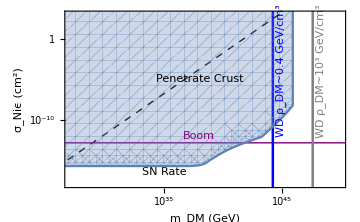

```mathematica
transitobservation=Show[canvastransit,crustplotTeV,photontransitTeV,fluxlimitRX,fluxlimitNuStar,SNtransitregionplot,Graphics[Inset[Style["Boom",Small,Purple,FontFamily->"Helvetica"],{38,-12},{0,0},4,{1,0}]],
Graphics[Inset[Style["SN Rate",Small,Black,FontFamily->"Helvetica"],{35,-16.5},{0,0},4,{1,0}]],Graphics[Inset[Style["WD ρ_DM~10^3 GeV/cm^3",Small,Gray,FontFamily->"Helvetica"],{48.3,-4},{0,0},12,{0,1}]],Graphics[Inset[Style["WD ρ_DM~0.4 GeV/cm^3",Small,Blue,FontFamily->"Helvetica"],{44.9,-4},{0,0},12,{0,1}]],Graphics[Inset[Style["Penetrate Crust",Small,FontFamily->"Helvetica"],{38,-5},{0,0},10,{1,3/4}]],ImageSize->Medium]
```

#### Competing constraints: deplete galactic halo by O(1), CMB polarization, terrestrial cosmic ray experiments, general DM decay.

```mathematica
σHalo=Convert[Barn/(ElectronVolt Giga)mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCMB=Convert[Convert[3 10^-26 Centimeter^3/Second*1/(100 Giga ElectronVolt) (((10 ElectronVolt)/(mdm Giga ElectronVolt))^(1/2)SpeedOfLight)^-1,Barn/(Giga ElectronVolt)]mdm Giga ElectronVolt/.mdm->10^logmdm,Centimeter^2] 1/Centimeter^2;
σCR=Convert[1/(5Year)*(((0.3 Giga ElectronVolt)/Centimeter^3 1/(mdm Giga ElectronVolt))^2 10^-3 SpeedOfLight*(50 Kilo Meter)^2(50 Kilo Parsec))^-1,Centimeter^2] 1/Centimeter^2/.mdm->10^logmdm;
τCR=Convert[(0.3 Giga ElectronVolt)/Centimeter^3*1/(mdm Giga ElectronVolt)*(50 Kilo Meter)^2(50 Kilo Parsec)*5Year,Giga Year] 1/(Giga Year)/.mdm->10^logmdm;
τcosmo=10^2 Giga Year*1/(Giga Year);
```

#### Plotting competing constraints

```mathematica
σHaloplot=Plot[Log10[σHalo],{logmdm,13,35},PlotStyle->{Red,Thick}];
τCosmoplot=Plot[Log10[τcosmo],{logmdm,13,35},PlotStyle->{Red,Thick}];
σCMBplot=Plot[Log10[σCMB],{logmdm,eboom[1.25],35},PlotStyle->{Green,Thick}];
σCRplot=Plot[Log10[σCR],{logmdm,eboom[1.25],35},PlotStyle->{Red,Thick}];
τCRplot=Plot[Log10[τCR],{logmdm,eboom[1.25],35},PlotStyle->{Cyan,Thick}];
```

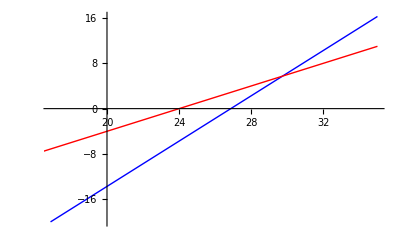

```mathematica
Show[RXcollision,σHaloplot]
```

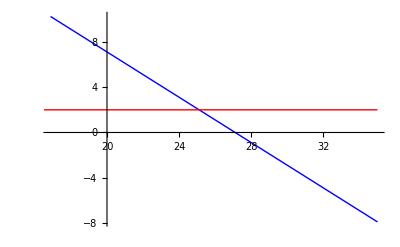

```mathematica
Show[RXdecay,τCosmoplot]
```

#### Q-ball boom σ_Q

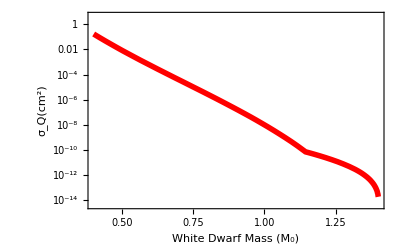

```mathematica
LogPlot[transitboom[M]/.ϵ->10^4,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

#### SUSY Q-ball constraints, m_s=10^3 Gev

```mathematica
Log10[(1/π 10^-12 cm^2)^2(0.2 GeV 10^-13 cm)^-4(10^3 GeV)^4]
```

41.8016

```mathematica
(10^3 GeV)((1/π 10^-12 cm^2)^2(0.2 GeV 10^-13 cm)^-4(10^3 GeV)^4)^(3/4)
```

2.24484×10^34 GeV

```mathematica
transitNuStar
```

47.6593

```mathematica
Log10[((10^transitRX GeV)/(10^3 GeV))^(4/3)]
```

55.0151

```mathematica
Log10[((10^43 GeV)/(10^3 GeV))^(4/3)]//N
```

53.3333

```mathematica
Log10[((10^19 GeV)/(10^3 GeV))^4]
```

64

```mathematica
Solve[{m==ms Q^(3/4),σ==π Q^(1/2)/ms^2},{Q,ms}]
```

```mathematica
{Q->(m √σ)/(√π),ms->(m^(1/4) π^(3/8))/σ^(3/8)}
```

```mathematica
Qballreverse=Interpolation[Table[{Log10[transitboom[M]],M}/.{ϵ->10^4},{M,0.4,1.4,0.01}],InterpolationOrder->1];
Qballintegral[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi (restrict Radplot[x])^2 10^10 whitedwarfdistribution[x],{x,(If[Qballreverse[logσ]≥0.85,Qballreverse[logσ], 0.85]),1.40}]]
```

```mathematica
Log10[transitboom[1.3999]]/.ϵ->10^4
```

-13.7612

```mathematica
Log10[transitboom[0.85]]/.ϵ->10^4
```

-6.13791

```mathematica
Log10[unitlesstransit Qballintegral[Log10[transitboom[1.3999]]/.ϵ->10^4]]
```

36.9683

```mathematica
Log10[unitlesstransit Qballintegral[Log10[transitboom[0.85]]/.ϵ->10^4]]
```

46.0239

```mathematica
Log10[unitlesstransit Qballintegral[-13.76119878196517]]
```

36.9683

```mathematica
QballSNtable=Table[{Log10[unitlesstransit Qballintegral[logσ]],logσ},{logσ,Log10[transitboom[1.3999]]/.ϵ->10^4,Log10[transitboom[0.85]]/.ϵ->10^4,0.01}]
```

{{36.9683,-13.7612},{37.2352,-13.7512},{37.4004,-13.7412},{37.5207,-13.7312},{37.6154,-13.7212},{37.6937,-13.7112},{37.7605,-13.7012},{37.8189,-13.6912},{37.8706,-13.6812},{37.9173,-13.6712},{37.9596,-13.6612},{37.9986,-13.6512},{38.0345,-13.6412},{38.068,-13.6312},{38.0993,-13.6212},{38.1287,-13.6112},{38.1564,-13.6012},{38.1827,-13.5912},{38.2076,-13.5812},{38.2314,-13.5712},{38.2541,-13.5612},{38.2758,-13.5512},{38.2966,-13.5412},{38.3166,-13.5312},{38.3359,-13.5212},{38.3545,-13.5112},{38.3724,-13.5012},{38.3897,-13.4912},{38.4065,-13.4812},{38.4228,-13.4712},{38.4385,-13.4612},{38.4539,-13.4512},{38.4688,-13.4412},{38.4832,-13.4312},{38.4974,-13.4212},{38.5111,-13.4112},{38.5245,-13.4012},{38.5376,-13.3912},{38.5504,-13.3812},{38.5629,-13.3712},{38.5751,-13.3612},{38.5871,-13.3512},{38.5988,-13.3412},{38.6103,-13.3312},{38.6215,-13.3212},{38.6325,-13.3112},{38.6433,-13.3012},{38.6539,-13.2912},{38.6644,-13.2812},{38.6746,-13.2712},{38.6847,-13.2612},{38.6946,-13.2512},{38.7044,-13.2412},{38.714,-13.2312},{38.7235,-13.2212},{38.7328,-13.2112},{38.742,-13.2012},{38.7511,-13.1912},{38.76,-13.1812},{38.7688,-13.1712},{38.7775,-13.1612},{38.7861,-13.1512},{38.7946,-13.1412},{38.803,-13.1312},{38.8113,-13.1212},{38.8194,-13.1112},{38.8275,-13.1012},{38.8355,-13.0912},{38.8434,-13.0812},{38.8512,-13.0712},{38.8589,-13.0612},{38.8665,-13.0512},{38.874,-13.0412},{38.8815,-13.0312},{38.8889,-13.0212},{38.8962,-13.0112},{38.9034,-13.0012},{38.9174,-12.9912},{38.9324,-12.9812},{38.9471,-12.9712},{38.9616,-12.9612},{38.9758,-12.9512},{38.9897,-12.9412},{39.0034,-12.9312},{39.0169,-12.9212},{39.0301,-12.9112},{39.0431,-12.9012},{39.0559,-12.8912},{39.0685,-12.8812},{39.081,-12.8712},{39.0932,-12.8612},{39.1053,-12.8512},{39.1172,-12.8412},{39.129,-12.8312},{39.1406,-12.8212},{39.1521,-12.8112},{39.1634,-12.8012},{39.1746,-12.7912},{39.1856,-12.7812},{39.1965,-12.7712},{39.2073,-12.7612},{39.218,-12.7512},{39.2286,-12.7412},{39.239,-12.7312},{39.2494,-12.7212},{39.2596,-12.7112},{39.2697,-12.7012},{39.2798,-12.6912},{39.2897,-12.6812},{39.2996,-12.6712},{39.3093,-12.6612},{39.319,-12.6512},{39.3286,-12.6412},{39.341,-12.6312},{39.3538,-12.6212},{39.3665,-12.6112},{39.3791,-12.6012},{39.3915,-12.5912},{39.4038,-12.5812},{39.4159,-12.5712},{39.428,-12.5612},{39.4399,-12.5512},{39.4517,-12.5412},{39.4634,-12.5312},{39.475,-12.5212},{39.4865,-12.5112},{39.4979,-12.5012},{39.5092,-12.4912},{39.5204,-12.4812},{39.5315,-12.4712},{39.5425,-12.4612},{39.5534,-12.4512},{39.5643,-12.4412},{39.5751,-12.4312},{39.5858,-12.4212},{39.5964,-12.4112},{39.6069,-12.4012},{39.6174,-12.3912},{39.6278,-12.3812},{39.6395,-12.3712},{39.6523,-12.3612},{39.6651,-12.3512},{39.6778,-12.3412},{39.6903,-12.3312},{39.7028,-12.3212},{39.7152,-12.3112},{39.7275,-12.3012},{39.7397,-12.2912},{39.7518,-12.2812},{39.7639,-12.2712},{39.7758,-12.2612},{39.7877,-12.2512},{39.7996,-12.2412},{39.8113,-12.2312},{39.823,-12.2212},{39.8346,-12.2112},{39.8461,-12.2012},{39.8576,-12.1912},{39.869,-12.1812},{39.8804,-12.1712},{39.8929,-12.1612},{39.9062,-12.1512},{39.9194,-12.1412},{39.9326,-12.1312},{39.9457,-12.1212},{39.9587,-12.1112},{39.9717,-12.1012},{39.9845,-12.0912},{39.9973,-12.0812},{40.0101,-12.0712},{40.0228,-12.0612},{40.0354,-12.0512},{40.0479,-12.0412},{40.0604,-12.0312},{40.0729,-12.0212},{40.0852,-12.0112},{40.0976,-12.0012},{40.1098,-11.9912},{40.1234,-11.9812},{40.1369,-11.9712},{40.1505,-11.9612},{40.1639,-11.9512},{40.1774,-11.9412},{40.1907,-11.9312},{40.204,-11.9212},{40.2172,-11.9112},{40.2304,-11.9012},{40.2435,-11.8912},{40.2566,-11.8812},{40.2696,-11.8712},{40.2826,-11.8612},{40.2955,-11.8512},{40.3084,-11.8412},{40.3214,-11.8312},{40.3359,-11.8212},{40.3503,-11.8112},{40.3646,-11.8012},{40.3789,-11.7912},{40.3931,-11.7812},{40.4073,-11.7712},{40.4214,-11.7612},{40.4355,-11.7512},{40.4495,-11.7412},{40.4635,-11.7312},{40.4774,-11.7212},{40.4913,-11.7112},{40.5051,-11.7012},{40.5192,-11.6912},{40.5343,-11.6812},{40.5493,-11.6712},{40.5644,-11.6612},{40.5793,-11.6512},{40.5942,-11.6412},{40.6091,-11.6312},{40.6239,-11.6212},{40.6386,-11.6112},{40.6534,-11.6012},{40.668,-11.5912},{40.6827,-11.5812},{40.6972,-11.5712},{40.7123,-11.5612},{40.728,-11.5512},{40.7435,-11.5412},{40.7591,-11.5312},{40.7746,-11.5212},{40.79,-11.5112},{40.8054,-11.5012},{40.8207,-11.4912},{40.836,-11.4812},{40.8513,-11.4712},{40.8665,-11.4612},{40.8817,-11.4512},{40.8978,-11.4412},{40.9142,-11.4312},{40.9305,-11.4212},{40.9468,-11.4112},{40.9631,-11.4012},{40.9793,-11.3912},{40.9954,-11.3812},{41.0115,-11.3712},{41.0276,-11.3612},{41.0436,-11.3512},{41.0596,-11.3412},{41.0768,-11.3312},{41.094,-11.3212},{41.1111,-11.3112},{41.1282,-11.3012},{41.1452,-11.2912},{41.1622,-11.2812},{41.1792,-11.2712},{41.196,-11.2612},{41.2129,-11.2512},{41.2297,-11.2412},{41.2471,-11.2312},{41.2645,-11.2212},{41.2818,-11.2112},{41.299,-11.2012},{41.3163,-11.1912},{41.3335,-11.1812},{41.3506,-11.1712},{41.3677,-11.1612},{41.3847,-11.1512},{41.4018,-11.1412},{41.4191,-11.1312},{41.4363,-11.1212},{41.4535,-11.1112},{41.4706,-11.1012},{41.4877,-11.0912},{41.5048,-11.0812},{41.5218,-11.0712},{41.5387,-11.0612},{41.5557,-11.0512},{41.5737,-11.0412},{41.5919,-11.0312},{41.61,-11.0212},{41.628,-11.0112},{41.646,-11.0012},{41.664,-10.9912},{41.6819,-10.9812},{41.6998,-10.9712},{41.7178,-10.9612},{41.7367,-10.9512},{41.7555,-10.9412},{41.7744,-10.9312},{41.7931,-10.9212},{41.8118,-10.9112},{41.8305,-10.9012},{41.8491,-10.8912},{41.8677,-10.8812},{41.8867,-10.8712},{41.9057,-10.8612},{41.9247,-10.8512},{41.9436,-10.8412},{41.9624,-10.8312},{41.9813,-10.8212},{42.,-10.8112},{42.0187,-10.8012},{42.0379,-10.7912},{42.0572,-10.7812},{42.0764,-10.7712},{42.0955,-10.7612},{42.1146,-10.7512},{42.1337,-10.7412},{42.1527,-10.7312},{42.1717,-10.7212},{42.1913,-10.7112},{42.2108,-10.7012},{42.2303,-10.6912},{42.2497,-10.6812},{42.2691,-10.6712},{42.2885,-10.6612},{42.3078,-10.6512},{42.3273,-10.6412},{42.3471,-10.6312},{42.3669,-10.6212},{42.3866,-10.6112},{42.4062,-10.6012},{42.4258,-10.5912},{42.4454,-10.5812},{42.465,-10.5712},{42.485,-10.5612},{42.5049,-10.5512},{42.5247,-10.5412},{42.5445,-10.5312},{42.5643,-10.5212},{42.584,-10.5112},{42.6037,-10.5012},{42.6239,-10.4912},{42.6439,-10.4812},{42.664,-10.4712},{42.6839,-10.4612},{42.7038,-10.4512},{42.7237,-10.4412},{42.7436,-10.4312},{42.7639,-10.4212},{42.7842,-10.4112},{42.8044,-10.4012},{42.8245,-10.3912},{42.8445,-10.3812},{42.8645,-10.3712},{42.8848,-10.3612},{42.9053,-10.3512},{42.9257,-10.3412},{42.946,-10.3312},{42.9662,-10.3212},{42.9864,-10.3112},{43.0066,-10.3012},{43.0273,-10.2912},{43.0478,-10.2812},{43.0683,-10.2712},{43.0887,-10.2612},{43.1091,-10.2512},{43.1294,-10.2412},{43.1501,-10.2312},{43.1709,-10.2212},{43.1916,-10.2112},{43.2123,-10.2012},{43.2329,-10.1912},{43.2534,-10.1812},{43.2682,-10.1712},{43.28,-10.1612},{43.2918,-10.1512},{43.3036,-10.1412},{43.3153,-10.1312},{43.327,-10.1212},{43.3387,-10.1112},{43.3504,-10.1012},{43.3621,-10.0912},{43.3737,-10.0812},{43.3853,-10.0712},{43.3928,-10.0612},{43.4002,-10.0512},{43.4076,-10.0412},{43.4149,-10.0312},{43.4223,-10.0212},{43.4297,-10.0112},{43.437,-10.0012},{43.4444,-9.9912},{43.4517,-9.9812},{43.459,-9.9712},{43.4663,-9.9612},{43.4736,-9.9512},{43.4809,-9.9412},{43.4882,-9.9312},{43.4955,-9.9212},{43.5028,-9.9112},{43.51,-9.9012},{43.5173,-9.8912},{43.5246,-9.8812},{43.5319,-9.8712},{43.5392,-9.8612},{43.5464,-9.8512},{43.5537,-9.8412},{43.5609,-9.8312},{43.5682,-9.8212},{43.5754,-9.8112},{43.5826,-9.8012},{43.5898,-9.7912},{43.597,-9.7812},{43.6042,-9.7712},{43.6114,-9.7612},{43.6186,-9.7512},{43.6257,-9.7412},{43.633,-9.7312},{43.6403,-9.7212},{43.6476,-9.7112},{43.6548,-9.7012},{43.6621,-9.6912},{43.6694,-9.6812},{43.6766,-9.6712},{43.6839,-9.6612},{43.6911,-9.6512},{43.6983,-9.6412},{43.7055,-9.6312},{43.7128,-9.6212},{43.72,-9.6112},{43.7271,-9.6012},{43.7343,-9.5912},{43.7415,-9.5812},{43.7488,-9.5712},{43.7562,-9.5612},{43.7635,-9.5512},{43.7709,-9.5412},{43.7783,-9.5312},{43.7856,-9.5212},{43.7929,-9.5112},{43.8003,-9.5012},{43.8076,-9.4912},{43.8149,-9.4812},{43.8222,-9.4712},{43.8295,-9.4612},{43.8368,-9.4512},{43.8441,-9.4412},{43.8513,-9.4312},{43.8586,-9.4212},{43.866,-9.4112},{43.8735,-9.4012},{43.8809,-9.3912},{43.8884,-9.3812},{43.8958,-9.3712},{43.9033,-9.3612},{43.9107,-9.3512},{43.9181,-9.3412},{43.9255,-9.3312},{43.9329,-9.3212},{43.9403,-9.3112},{43.9477,-9.3012},{43.9551,-9.2912},{43.9624,-9.2812},{43.9698,-9.2712},{43.9772,-9.2612},{43.9847,-9.2512},{43.9921,-9.2412},{43.9996,-9.2312},{44.0071,-9.2212},{44.0145,-9.2112},{44.0219,-9.2012},{44.0294,-9.1912},{44.0368,-9.1812},{44.0442,-9.1712},{44.0516,-9.1612},{44.059,-9.1512},{44.0663,-9.1412},{44.0737,-9.1312},{44.0811,-9.1212},{44.0885,-9.1112},{44.0959,-9.1012},{44.1034,-9.0912},{44.1108,-9.0812},{44.1182,-9.0712},{44.1257,-9.0612},{44.1331,-9.0512},{44.1404,-9.0412},{44.1478,-9.0312},{44.1552,-9.0212},{44.1626,-9.0112},{44.1699,-9.0012},{44.1772,-8.9912},{44.1846,-8.9812},{44.1919,-8.9712},{44.1993,-8.9612},{44.2067,-8.9512},{44.2141,-8.9412},{44.2215,-8.9312},{44.2288,-8.9212},{44.2362,-8.9112},{44.2435,-8.9012},{44.2509,-8.8912},{44.2582,-8.8812},{44.2655,-8.8712},{44.2728,-8.8612},{44.2801,-8.8512},{44.2874,-8.8412},{44.2946,-8.8312},{44.3019,-8.8212},{44.3093,-8.8112},{44.3166,-8.8012},{44.324,-8.7912},{44.3313,-8.7812},{44.3386,-8.7712},{44.3459,-8.7612},{44.3531,-8.7512},{44.3604,-8.7412},{44.3677,-8.7312},{44.3749,-8.7212},{44.3822,-8.7112},{44.3894,-8.7012},{44.3966,-8.6912},{44.4038,-8.6812},{44.4111,-8.6712},{44.4183,-8.6612},{44.4256,-8.6512},{44.4328,-8.6412},{44.44,-8.6312},{44.4472,-8.6212},{44.4544,-8.6112},{44.4616,-8.6012},{44.4688,-8.5912},{44.476,-8.5812},{44.4831,-8.5712},{44.4903,-8.5612},{44.4974,-8.5512},{44.5045,-8.5412},{44.5117,-8.5312},{44.5189,-8.5212},{44.526,-8.5112},{44.5332,-8.5012},{44.5403,-8.4912},{44.5475,-8.4812},{44.5546,-8.4712},{44.5617,-8.4612},{44.5688,-8.4512},{44.5759,-8.4412},{44.5829,-8.4312},{44.59,-8.4212},{44.5971,-8.4112},{44.6041,-8.4012},{44.6112,-8.3912},{44.6183,-8.3812},{44.6254,-8.3712},{44.6325,-8.3612},{44.6396,-8.3512},{44.6467,-8.3412},{44.6537,-8.3312},{44.6608,-8.3212},{44.6678,-8.3112},{44.6748,-8.3012},{44.6818,-8.2912},{44.6888,-8.2812},{44.6958,-8.2712},{44.7028,-8.2612},{44.7099,-8.2512},{44.717,-8.2412},{44.7241,-8.2312},{44.7311,-8.2212},{44.7381,-8.2112},{44.7452,-8.2012},{44.7522,-8.1912},{44.7592,-8.1812},{44.7662,-8.1712},{44.7732,-8.1612},{44.7801,-8.1512},{44.7871,-8.1412},{44.794,-8.1312},{44.801,-8.1212},{44.8081,-8.1112},{44.8151,-8.1012},{44.8221,-8.0912},{44.8291,-8.0812},{44.836,-8.0712},{44.843,-8.0612},{44.85,-8.0512},{44.8569,-8.0412},{44.8638,-8.0312},{44.8707,-8.0212},{44.8776,-8.0112},{44.8845,-8.0012},{44.8915,-7.9912},{44.8984,-7.9812},{44.9053,-7.9712},{44.9122,-7.9612},{44.9191,-7.9512},{44.926,-7.9412},{44.9329,-7.9312},{44.9398,-7.9212},{44.9466,-7.9112},{44.9535,-7.9012},{44.9603,-7.8912},{44.9671,-7.8812},{44.9739,-7.8712},{44.9807,-7.8612},{44.9875,-7.8512},{44.9943,-7.8412},{45.0011,-7.8312},{45.0078,-7.8212},{45.0146,-7.8112},{45.0213,-7.8012},{45.028,-7.7912},{45.0347,-7.7812},{45.0414,-7.7712},{45.0481,-7.7612},{45.0548,-7.7512},{45.0615,-7.7412},{45.0681,-7.7312},{45.0748,-7.7212},{45.0815,-7.7112},{45.0881,-7.7012},{45.0948,-7.6912},{45.1014,-7.6812},{45.108,-7.6712},{45.1146,-7.6612},{45.1212,-7.6512},{45.1278,-7.6412},{45.1344,-7.6312},{45.1409,-7.6212},{45.1475,-7.6112},{45.154,-7.6012},{45.1606,-7.5912},{45.1672,-7.5812},{45.1738,-7.5712},{45.1803,-7.5612},{45.1869,-7.5512},{45.1934,-7.5412},{45.1999,-7.5312},{45.2064,-7.5212},{45.2129,-7.5112},{45.2194,-7.5012},{45.2259,-7.4912},{45.2323,-7.4812},{45.2388,-7.4712},{45.2454,-7.4612},{45.2519,-7.4512},{45.2584,-7.4412},{45.2649,-7.4312},{45.2714,-7.4212},{45.2779,-7.4112},{45.2844,-7.4012},{45.2908,-7.3912},{45.2973,-7.3812},{45.3037,-7.3712},{45.3101,-7.3612},{45.3165,-7.3512},{45.323,-7.3412},{45.3295,-7.3312},{45.3359,-7.3212},{45.3424,-7.3112},{45.3488,-7.3012},{45.3552,-7.2912},{45.3616,-7.2812},{45.368,-7.2712},{45.3744,-7.2612},{45.3808,-7.2512},{45.3871,-7.2412},{45.3935,-7.2312},{45.3998,-7.2212},{45.4062,-7.2112},{45.4125,-7.2012},{45.4189,-7.1912},{45.4252,-7.1812},{45.4315,-7.1712},{45.4378,-7.1612},{45.4441,-7.1512},{45.4504,-7.1412},{45.4567,-7.1312},{45.4629,-7.1212},{45.4691,-7.1112},{45.4754,-7.1012},{45.4816,-7.0912},{45.4878,-7.0812},{45.494,-7.0712},{45.5002,-7.0612},{45.5064,-7.0512},{45.5126,-7.0412},{45.5187,-7.0312},{45.5249,-7.0212},{45.531,-7.0112},{45.5371,-7.0012},{45.5432,-6.9912},{45.5493,-6.9812},{45.5554,-6.9712},{45.5615,-6.9612},{45.5676,-6.9512},{45.5736,-6.9412},{45.5797,-6.9312},{45.5857,-6.9212},{45.5917,-6.9112},{45.5977,-6.9012},{45.6037,-6.8912},{45.6097,-6.8812},{45.6157,-6.8712},{45.6216,-6.8612},{45.6276,-6.8512},{45.6336,-6.8412},{45.6395,-6.8312},{45.6455,-6.8212},{45.6514,-6.8112},{45.6573,-6.8012},{45.6632,-6.7912},{45.6691,-6.7812},{45.675,-6.7712},{45.6808,-6.7612},{45.6867,-6.7512},{45.6925,-6.7412},{45.6983,-6.7312},{45.7042,-6.7212},{45.71,-6.7112},{45.7159,-6.7012},{45.7217,-6.6912},{45.7275,-6.6812},{45.7332,-6.6712},{45.739,-6.6612},{45.7448,-6.6512},{45.7505,-6.6412},{45.7562,-6.6312},{45.7619,-6.6212},{45.7676,-6.6112},{45.7734,-6.6012},{45.7791,-6.5912},{45.7848,-6.5812},{45.7904,-6.5712},{45.7961,-6.5612},{45.8017,-6.5512},{45.8074,-6.5412},{45.813,-6.5312},{45.8186,-6.5212},{45.8242,-6.5112},{45.8298,-6.5012},{45.8353,-6.4912},{45.8409,-6.4812},{45.8465,-6.4712},{45.852,-6.4612},{45.8575,-6.4512},{45.8631,-6.4412},{45.8686,-6.4312},{45.874,-6.4212},{45.8795,-6.4112},{45.885,-6.4012},{45.8904,-6.3912},{45.8959,-6.3812},{45.9013,-6.3712},{45.9067,-6.3612},{45.9121,-6.3512},{45.9174,-6.3412},{45.9228,-6.3312},{45.9281,-6.3212},{45.9335,-6.3112},{45.9388,-6.3012},{45.9441,-6.2912},{45.9494,-6.2812},{45.9547,-6.2712},{45.9599,-6.2612},{45.9652,-6.2512},{45.9704,-6.2412},{45.9757,-6.2312},{45.9809,-6.2212},{45.9861,-6.2112},{45.9913,-6.2012},{45.9965,-6.1912},{46.0017,-6.1812},{46.0068,-6.1712},{46.012,-6.1612},{46.0171,-6.1512},{46.0222,-6.1412}}

```mathematica
QballSN=Interpolation[Table[{Log10[unitlesstransit Qballintegral[logσ]],logσ},{logσ,Log10[transitboom[1.3999]]/.ϵ->10^4,Log10[transitboom[0.85]]/.ϵ->10^4,0.01}]];
```

```mathematica
Log10[unitlesstransit Qballintegral[Log10[transitboom[1.3999]]/.ϵ->10^4]]
```

36.9683

```mathematica
Log10[transitboom[1.3999]]/.ϵ->10^4
```

-13.7612

```mathematica
Qballwhole[logmdm_]:=If[logmdm≤36.96826877174541,-13.76119878196517,QballSN[logmdm]]
```

```mathematica
logms=Log10[FullSimplify[(m^(1/4) π^(3/8))/σ^(3/8)(0.2GeV 10^-13 cm)^(3/4)/.{m->10^logmdm GeV,σ->10^logσ cm^2},{GeV>0,cm>0}]*1/GeV]/.logσ->Qballwhole[logmdm];
```

```mathematica
logQ=Log10[FullSimplify[(m √σ)/(√π)(0.2GeV 10^-13 cm)^-1/.{m->10^logmdm GeV,σ->10^logσ cm^2},cm>0]]/.logσ->Qballwhole[logmdm];
```

```mathematica
q=Log10[((10^Log10[unitlesstransit Qballintegral[Log10[transitboom[0.85]]/.ϵ->10^4]])/10^ms)^(4/3)];
```

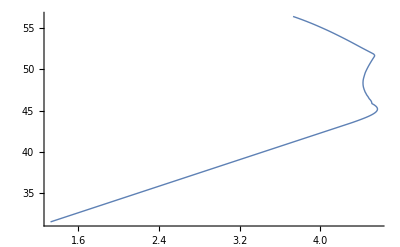

```mathematica
normalSN=ListPlot[Table[{logms,logQ},{logmdm,25,46,0.1}],Joined->True,PlotStyle->{Thick}]
```

```mathematica
endSN=Plot[q,{ms,1,3.74},PlotStyle->{Thick}];
```